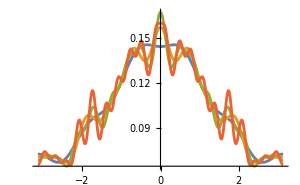

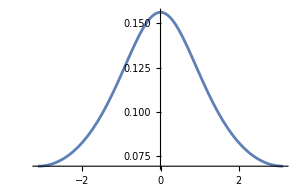

```mathematica
data=RandomFunction[ARProcess[{.2},.1],{1,5000}];
Plot[Evaluate@Table[PowerSpectralDensity[data,ω,i],{i,5,20,5}],{ω,-π,π},PlotRange->All,ImageSize->300]
Plot[PowerSpectralDensity[ARProcess[{.2},.1],ω],{ω,-π,π},PlotRange->All,ImageSize->300]
```